# HextileBins

Bin data into hexagon tiles

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

### Support functions

```mathematica
Clear[ReferenceHexagon];
ReferenceHexagon[]:={{1/2,Sqrt[3]/2},{-(1/2),Sqrt[3]/2},{-1,0},{-(1/2),-(Sqrt[3]/2)},{1/2,-(Sqrt[3]/2)},{1,0}};

Clear[NearestWithinTile];
NearestWithinTile=Nearest[{{0,0},{1,0},{1/2,Sqrt[3]/2},{0,Sqrt[3]},{1,Sqrt[3]}}];

Clear[TileContaining];
TileContaining[{x_,y_}]:={Floor[x],Sqrt[3] Floor[y/Sqrt[3]]};

Clear[NearestHexagon];
NearestHexagon[point:{_?NumericQ,_?NumericQ}]:=Module[{tile,relative},tile=TileContaining[point];
relative=point-tile;
tile+First@NearestWithinTile[relative]];

Clear[TransformByVector];
TransformByVector[v_,tr_]:=Polygon[TranslationTransform[tr][RotationTransform[Pi/2][v]]];

Clear[HexagonVertexDistance];
HexagonVertexDistance[binSize_?NumericQ]:=binSize*1.0*ReferenceHexagon[]/Sqrt[3];

Clear[HextileBinDataRulesQ];
HextileBinDataRulesQ[d_]:=MatchQ[d,(List|Association)[({_?NumericQ,_?NumericQ}->_?NumericQ)..]];

Clear[HextileBinDataQ];
HextileBinDataQ[d_]:=(MatrixQ[d]&&Dimensions[d][[2]]==2)||HextileBinDataRulesQ[d];
```

### HextileCenterBins

```mathematica
Clear[HextileCenterBins];

SyntaxInformation[HextileCenterBins]={"ArgumentsPattern"->{_,_,_.,OptionsPattern[]}};

Options[HextileCenterBins]={"AggregationFunction"->Total};

HextileCenterBins[data_?HextileBinDataQ,binSize_?NumericQ,opts:OptionsPattern[]]:=HextileCenterBins[data,binSize,Automatic,opts];

HextileCenterBins[data_?MatrixQ,binSize_?NumericQ,Automatic,opts:OptionsPattern[]]:=HextileCenterBins[data,binSize,MinMax/@Transpose[data],opts]/;Dimensions[data][[2]]==2;

HextileCenterBins[data_?MatrixQ,binSize_?NumericQ,{{xmin_,xmax_},{ymin_,ymax_}},opts:OptionsPattern[]]:=
Block[{},
Association[Rule@@@Tally[binSize*(NearestHexagon/@(data/binSize))]]
]/;Dimensions[data][[2]]==2;

HextileCenterBins[data_?HextileBinDataRulesQ,binSize_?NumericQ,Automatic,opts:OptionsPattern[]]:=HextileCenterBins[data,binSize,MinMax/@Transpose[Keys[data]],opts];

HextileCenterBins[data_?HextileBinDataRulesQ,binSize_?NumericQ,{{xmin_,xmax_},{ymin_,ymax_}},opts:OptionsPattern[]]:=
Block[{aggrFunc},
aggrFunc=OptionValue[HextileCenterBins,"AggregationFunction"];
GroupBy[Map[(binSize*NearestHexagon[#[[1]]/binSize])->#[[2]]&,Normal[data]],#[[1]]&,aggrFunc[#[[All,2]]]&]
];
```

### HextilePolygonBins

```mathematica
Clear[HextilePolygonBins];

SyntaxInformation[HextilePolygonBins]={"ArgumentsPattern"->{_,_,_.,OptionsPattern[]}};

Options[HextilePolygonBins]=Options[HextileCenterBins];

HextilePolygonBins[data_?HextileBinDataQ,binSize_?NumericQ,opts:OptionsPattern[]]:=HextilePolygonBins[data,binSize,Automatic,opts];

HextilePolygonBins[data_?HextileBinDataQ,binSize_?NumericQ,Automatic,opts:OptionsPattern[]]:=HextilePolygonBins[data,binSize,If[MatrixQ[data],MinMax/@Transpose[data],MinMax/@Transpose[Keys[data]]],opts];

HextilePolygonBins[data_?HextileBinDataQ,binSize_?NumericQ,{{xmin_,xmax_},{ymin_,ymax_}},opts:OptionsPattern[]]:=Block[{vh=HexagonVertexDistance[binSize]},KeyMap[TransformByVector[vh,#]&,HextileCenterBins[data,binSize,{{xmin,xmax},{ymin,ymax}},opts]]];
```

### HextileBins

```mathematica
Clear[HextileBins];
```

```mathematica
SyntaxInformation[HextileBins]={"ArgumentsPattern"->{_,_,_.,OptionsPattern[]}};
```

```mathematica
HextileBins::"nargs"="The first argument is expected to be a numerical matrix or an association of 2D coordinates to numeric values. The second argument is expected to be a positive number. The third argument is expected to be a range specification, two pairs of numbers, or Automatic.";
```

```mathematica
Options[HextileBins]={"AggregationFunction"->Total,"PolygonKeys"->True};
```

```mathematica
HextileBins[data_?HextileBinDataQ,binSize_?NumericQ,opts:OptionsPattern[]]:=HextileBins[data,binSize,Automatic,opts];
```

```mathematica
HextileBins[data_?HextileBinDataQ,binSize_?NumericQ,Automatic,opts:OptionsPattern[]]:=HextileBins[data,binSize,If[MatrixQ[data],MinMax/@Transpose[data],MinMax/@Transpose[Keys[data]]],opts];
```

```mathematica
HextileBins[data_?HextileBinDataQ,binSize_?NumericQ,{{xmin_,xmax_},{ymin_,ymax_}},opts:OptionsPattern[]]:=
Block[{polygonKeys},
polygonKeys=OptionValue[HextileBins,"PolygonKeys"];
If[BooleanQ[polygonKeys]&&!polygonKeys,
HextileCenterBins[data,binSize,{{xmin,xmax},{ymin,ymax}},FilterRules[{opts},Options[HextileCenterBins]]],
(*ELSE*)
HextilePolygonBins[data,binSize,{{xmin,xmax},{ymin,ymax}},FilterRules[{opts},Options[HextilePolygonBins]]]]
]/;binSize>0;
```

```mathematica
HextileBins[___]:=
Block[{},
Message[HextileBins::"nargs"];
$Failed
];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

HextileBins[mat,r]

bins a numerical full 2D array mat into hexagon grid tiles with radius r.

HextileBins[cv,r]

bins coordinates-to-value rules cv.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

HextileBins bins data into hexagon tiles.

The result is an association with keys that are polygon objects.

If the option "PolygonKeys" is set to False then the keys of the result are hexagon centers.

The option "AggregationFunction" is used to aggregate the values within each tile.

"AggregationFunction" | Total | function to aggegate the data in each tile
"PolygonKeys" | True | are the result keys polygons

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Create a list of random 2D points:

```mathematica
SeedRandom[113];
data=RandomVariate[MultinormalDistribution[{10,10},7*IdentityMatrix[2]],200];
```

Bin the points:

```mathematica
HextileBins[data,10]
```

<|Polygon[…]→87,Polygon[…]→79,Polygon[…]→30,Polygon[…]→4|>

Bin the points and get the hex-tile centers as keys:

```mathematica
HextileBins[data,10,"PolygonKeys"->False]
```

<|{5,5 √3}→87,{15,5 √3}→79,{10,10 √3}→30,{10,0}→4|>

Plot the points and the hexagon bins:

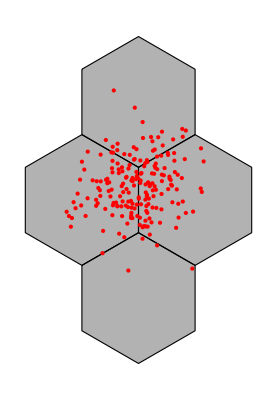

```mathematica
Graphics[{EdgeForm[Black],FaceForm[Opacity[0.3]],Keys@HextileBins[data,10],Red,Point[data]}]
```

### Scope

Associate random values to 2D data:

```mathematica
SeedRandom[113];
data=RandomVariate[MultinormalDistribution[{10,10},7*IdentityMatrix[2]],200];dataRules=AssociationThread[data,RandomReal[{0,1},Length[data]]];
```

Bin the data rules:

```mathematica
HextileBins[dataRules,10]
```

<|Polygon[…]→46.9921,Polygon[…]→38.1256,Polygon[…]→15.3234,Polygon[…]→1.44698|>

Bin the keys of the data rules:

```mathematica
HextileBins[Keys@dataRules,10]
```

<|Polygon[…]→87,Polygon[…]→79,Polygon[…]→30,Polygon[…]→4|>

Check the equivalence:

```mathematica
HextileBins[Keys@dataRules,10]==HextileBins[data,10]
```

True

### Options

#### AggregationFunction

Bin the data rules and compute average values on each tile:

```mathematica
SeedRandom[113];
data=RandomVariate[MultinormalDistribution[{10,10},7*IdentityMatrix[2]],200];dataRules=AssociationThread[data,RandomReal[{0,1},Length[data]]];
HextileBins[dataRules,6,"AggregationFunction"->Mean]
```

<|Polygon[…]→0.583159,Polygon[…]→0.494114,Polygon[…]→0.384244,Polygon[…]→0.373626,Polygon[…]→0.62687,Polygon[…]→0.444822,Polygon[…]→0.767265,Polygon[…]→0.448392|>

Compare with the default option value, Total:

```mathematica
HextileBins[dataRules,6,"AggregationFunction"->Total]
```

<|Polygon[…]→27.9916,Polygon[…]→40.5173,Polygon[…]→1.92122,Polygon[…]→1.12088,Polygon[…]→3.76122,Polygon[…]→16.0136,Polygon[…]→3.83632,Polygon[…]→6.72587|>

#### PolygonKeys

Instead of polygons as keys, you can get the centers of the polygons:

```mathematica
SeedRandom[113];
data=RandomVariate[MultinormalDistribution[{10,10},7*IdentityMatrix[2]],200];dataRules=AssociationThread[data,RandomReal[{0,1},Length[data]]];HextileBins[dataRules,10,"PolygonKeys"->False]
```

<|{5,5 √3}→46.9921,{15,5 √3}→38.1256,{10,10 √3}→15.3234,{10,0}→1.44698|>

### Applications

#### Data visualization

Generate data rules:

```mathematica
SeedRandom[113];
data2=RandomVariate[MultinormalDistribution[{10,10},7*IdentityMatrix[2]],300];dataRules2=AssociationThread[data2,RandomReal[{0,100},Length[data2]]];
```

Here we bin the data:

```mathematica
res2=HextileBins[dataRules2,2];
```

Plot points and hexagon bins by coloring each hexagon according to its aggregated value:

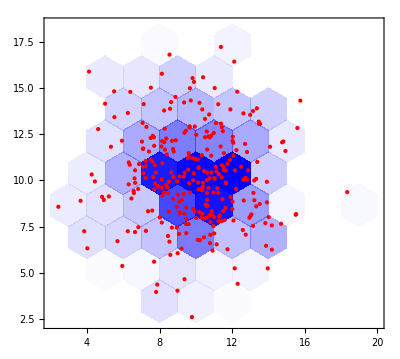

```mathematica
Graphics[{KeyValueMap[{FaceForm[Opacity[Rescale[#2,MinMax[Values[res2]],{0,1}],Blue]],#1}&,res2],Red,Point[Keys[dataRules2]]},Frame->True]
```

#### Make a hexagonal grid

You can make hexagonal grids:

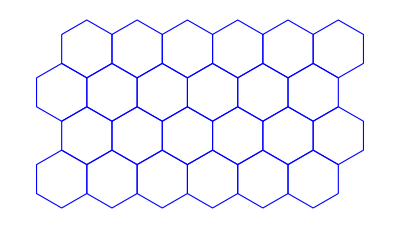

```mathematica
hexes=Keys@HextileBins[Flatten[Table[{x,y},{x,0,10},{y,0,5}],1],2];
Graphics[{EdgeForm[Blue],FaceForm[None],hexes}]
```

The coordinates of the polygons can be retrieved and transformed further:

```mathematica
Mean@*PolygonCoordinates/@hexes
```

{{0.,0.},{1.,1.73205},{0.,3.4641},{1.,5.19615},{2.,0.},{3.,1.73205},{2.,3.4641},{3.,5.19615},{4.,0.},{5.,1.73205},{4.,3.4641},{5.,5.19615},{6.,0.},{7.,1.73205},{6.,3.4641},{7.,5.19615},{8.,0.},{9.,1.73205},{8.,3.4641},{9.,5.19615},{10.,0.},{11.,1.73205},{10.,3.4641},{11.,5.19615}}

### Properties and Relations

The function GeoHistogram produces similar plots (in Version 12.1):

```mathematica
geoData=EntityValue[CountryData["Japan","LargestCities"],"Position"];
```

```mathematica
gr1=GeoHistogram[geoData,GeoProjection->"Equirectangular",Frame->True,PlotLabel->"GeoHistogram",ImageSize->250];
```

```mathematica
geoRes=HextileBins[Reverse[#⟦1⟧]&/@geoData,0.8];
gr2=Graphics[{KeyValueMap[{FaceForm[Blend[{Lighter[Lighter[Yellow]],Brown},Rescale[#2,MinMax[Values[geoRes]],{0,1}]]],#1}&,geoRes]},Frame->True,Prolog->{LightBlue,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},
PlotLabel->"HextileBins",ImageSize->250];
```

```mathematica
Row[{gr1,Spacer[10],gr2}]
```

-Graphics--Graphics-

The repository function HexagonalGridGraph can be also used to make hexagonal grids:

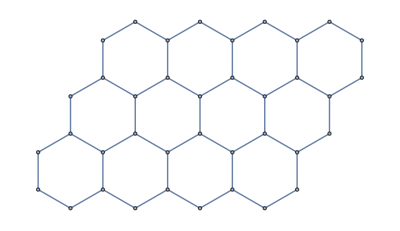

```mathematica
grHex=ResourceFunction["HexagonalGridGraph"][{4,3}]
```

Here are the corresponding coordinates:

```mathematica
GraphEmbedding[grHex]
```

{{0,0},{0,2},{√3,-1},{√3,3},{2 √3,0},{√3,5},{2 √3,2},{2 √3,6},{3 √3,-1},{3 √3,3},{2 √3,8},{3 √3,5},{3 √3,9},{4 √3,0},{4 √3,2},{4 √3,6},{4 √3,8},{5 √3,-1},{5 √3,3},{5 √3,5},{5 √3,9},{6 √3,0},{6 √3,2},{6 √3,6},{6 √3,8},{7 √3,-1},{7 √3,3},{7 √3,5},{7 √3,9},{8 √3,0},{8 √3,2},{8 √3,6},{8 √3,8},{9 √3,3},{9 √3,5},{9 √3,9},{10 √3,6},{10 √3,8}}

Here are the corresponding polygons:

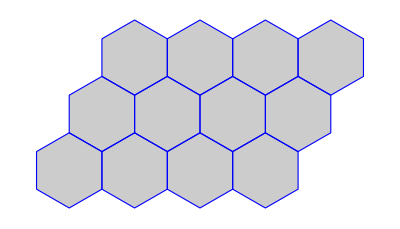

```mathematica
grHexPolygons=Map[Polygon@(List@@@#)⟦All,1⟧&,FindCycle[grHex,{6,6},All]];
Graphics[{EdgeForm[Blue],FaceForm[Opacity[0.2]],grHexPolygons}]
```

Make a similar grid with HextileBins:

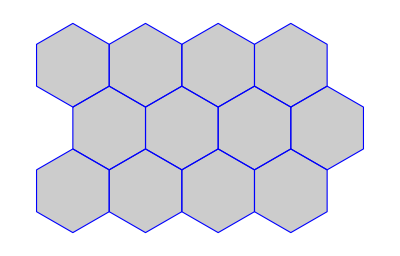

```mathematica
hexes2=Keys[HextileBins[Flatten[Table[{x,y},{x,0,6},{y,0,3}],1],2]];
Graphics[{EdgeForm[Blue],FaceForm[Opacity[0.2]],hexes2}]
```

Here are the corresponding coordinates:

```mathematica
Union[Join@@Map[PolygonCoordinates,hexes2]]
```

{{-1.,-0.57735},{-1.,0.57735},{-1.,2.88675},{-1.,4.04145},{0.,-1.1547},{0.,1.1547},{0.,1.1547},{0.,2.3094},{0.,4.6188},{1.,-0.57735},{1.,0.57735},{1.,0.57735},{1.,2.88675},{1.,2.88675},{1.,4.04145},{2.,-1.1547},{2.,1.1547},{2.,1.1547},{2.,2.3094},{2.,4.6188},{3.,-0.57735},{3.,0.57735},{3.,0.57735},{3.,2.88675},{3.,2.88675},{3.,4.04145},{4.,-1.1547},{4.,1.1547},{4.,1.1547},{4.,2.3094},{4.,4.6188},{5.,-0.57735},{5.,0.57735},{5.,0.57735},{5.,2.88675},{5.,2.88675},{5.,4.04145},{6.,-1.1547},{6.,1.1547},{6.,1.1547},{6.,2.3094},{6.,4.6188},{7.,-0.57735},{7.,0.57735},{7.,0.57735},{7.,2.88675},{7.,2.88675},{7.,4.04145},{8.,1.1547},{8.,2.3094}}

### Neat Examples

Bin data and summarize the values associated to bin centers:

```mathematica
SeedRandom[113];
data3=RandomVariate[MultinormalDistribution[{10,10},{1,1.7}*IdentityMatrix[2]],300];dataRules3=AssociationThread[data3,RandomReal[{0,100},Length[data3]]];
```

```mathematica
res=HextileBins[dataRules3,10,"PolygonKeys"->False,"AggregationFunction"->ResourceFunction["RecordsSummary"]]
```

<|{5,5 √3}→{1 column 1
Min | 1.37421
1st Qu | 23.7983
Median | 45.6596
Mean | 47.4009
3rd Qu | 73.4392
Max | 99.9737},{15,5 √3}→{1 column 1
Min | 0.165429
1st Qu | 21.5524
Median | 43.7795
Mean | 47.1144
3rd Qu | 73.3877
Max | 99.4322},{10,10 √3}→{1 column 1
Min | 3.55093
1st Qu | 24.4037
Median | 36.0124
Mean | 48.9587
3rd Qu | 84.3097
Max | 95.4377}|>

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Anton Antonov

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Hexagon

Hex-tile

3D histogram

Aggregation

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

GeoHistogram

BinCounts

BinLists

Polygon

Total

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

HexagonalGridGraph

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Source, reference or citation information

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Link to other related material

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Initial ideas/versions of the code of HextileBins can be found in Mathematica Stack Exchange:  https://mathematica.stackexchange.com/q/28149.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.